```mathematica
F[ivv_,ivh_,ihv_,ihh_]:=(ivv/ihv-ivh/ihh)/(ivv/ihv+2ivh/ihh);
```

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ihh]]
```

(3 ihv ivh ivv)/(2 ihv ivh+ihh ivv)^2

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ivh]]
```

-(3 ihh ihv ivv)/(2 ihv ivh+ihh ivv)^2

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ihv]]
```

-(3 ihh ivh ivv)/(2 ihv ivh+ihh ivv)^2

```mathematica
FullSimplify[D[F[ivv,ivh,ihv,ihh],ivv]]
```

(3 ihh ihv ivh)/(2 ihv ivh+ihh ivv)^2

data/mini.ods

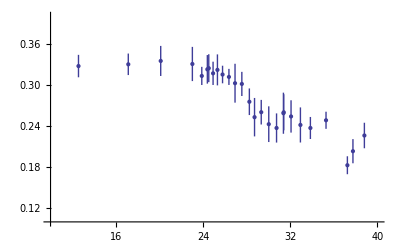

```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/mini.ods"])//TableForm
Needs["ErrorBarPlots`"]
Needs["ErrorBarPlots`"]
kotz2=First@Import[files[[1]]];
kotz2=kotz2[[2;;Length[kotz2]]];
ErrorListPlot[kotz2,PlotRange->{{10,40},{0.1,0.4}}]
```

```mathematica
kotz2//TableForm
```

12.565 | 0.327554 | 0.0163803
17.135 | 0.33013 | 0.0156964
20.11 | 0.335039 | 0.0219469
23.015 | 0.330594 | 0.0249699
23.88 | 0.313161 | 0.0132579
24.39 | 0.322775 | 0.0208592
24.52 | 0.324445 | 0.0203739
24.915 | 0.316954 | 0.0170022
25.315 | 0.321983 | 0.0226213
25.785 | 0.315222 | 0.0128423
26.37 | 0.311721 | 0.0117286
26.93 | 0.302525 | 0.0283827
27.555 | 0.301469 | 0.0176296
28.245 | 0.275442 | 0.0194297
28.72 | 0.252918 | 0.0280658
29.335 | 0.260198 | 0.0179556
30.025 | 0.242696 | 0.0260678
30.74 | 0.23714 | 0.021301
31.4 | 0.260066 | 0.0263834
31.37 | 0.258715 | 0.030012
32.07 | 0.253996 | 0.0236001
32.93 | 0.241565 | 0.0256164
33.845 | 0.237142 | 0.0160887
35.28 | 0.248393 | 0.0124993
37.24 | 0.182735 | 0.0130916
37.75 | 0.20324 | 0.0176344
38.8 | 0.226158 | 0.01863

```mathematica
kotz2[[1;;Length[kotz2]-3]]//TableForm
```

12.565 | 0.327554 | 0.0163803
17.135 | 0.33013 | 0.0156964
20.11 | 0.335039 | 0.0219469
23.015 | 0.330594 | 0.0249699
23.88 | 0.313161 | 0.0132579
24.39 | 0.322775 | 0.0208592
24.52 | 0.324445 | 0.0203739
24.915 | 0.316954 | 0.0170022
25.315 | 0.321983 | 0.0226213
25.785 | 0.315222 | 0.0128423
26.37 | 0.311721 | 0.0117286
26.93 | 0.302525 | 0.0283827
27.555 | 0.301469 | 0.0176296
28.245 | 0.275442 | 0.0194297
28.72 | 0.252918 | 0.0280658
29.335 | 0.260198 | 0.0179556
30.025 | 0.242696 | 0.0260678
30.74 | 0.23714 | 0.021301
31.4 | 0.260066 | 0.0263834
31.37 | 0.258715 | 0.030012
32.07 | 0.253996 | 0.0236001
32.93 | 0.241565 | 0.0256164
33.845 | 0.237142 | 0.0160887
35.28 | 0.248393 | 0.0124993

```mathematica
Join[kotz2[[1;;Length[kotz2]-3]]
```